# EFTwithFFT

To compute EFT 1-loop power spectrum observables, the FFTLog factorization is a common approach. Public packages that perform such computations include `CLASS-PT`, `pyBIRD`, and more recently, `ps_1loop_jax`. In this notebook, we follow the order of operations derived in EFTwithFFT_note.pdf. Specifically, we will derive the kernel corpus, validate the saved analytic kernels, build the linear-spectrum split and FFTLog decompositions, cache the raw one-loop sector objects, assemble the full anisotropic spectra P(k,mu), project to the ell=0,2,4 multipoles. This chain of operations closely mirrors the `ps_1loop_jax` approach. For comparison, we will first compare the symbolic kernels we derive here with the ones stored in `ps_1loop_jax` and then reproduce the plots in the `CLASS-PT` example notebook at `CLASS-PT/notebooks/nonlinear_pt.ipynb`. Heavy FFT work is cached once and reused across the no-IR, IR-resummed, and multipole sections.

## 1. Setup and Conventions

Load the package, freeze the ps_1loop_jax FFTLog bias conventions, and define the cosmology, nuisance parameters, and output grids used downstream.

```mathematica
SetDirectory@NotebookDirectory[];
Get[FileNameJoin[{NotebookDirectory[], "EFTwithFFT.wl"}]];

(* Parallel kernels for parallel evaluations, empirically did not find much improvement, so off by default *)
EFTwithFFT`$UseParallelForKernels = False;
EFTwithFFT`$UseParallelForMuIntegration = False;
EFTwithFFT`$UseParallelForMultipole = False;
EFTwithFFT`ClearFFTLogCache[];

(* Reference kernels in `ps_1loop_jax`*)
realSpaceReferenceDir = "./pt_matrix/real_space/gauss";
redshiftSpaceReferenceDir = "./pt_matrix/redshift_space/gauss";
(* Input linear matter power spectrum, in physical comoving unit *)
linearPath = "./Plin.dat";

(* FFTLog bias nu, follow the values in `ps_1loop_jax` *)
nuBiases = EFTwithFFT`Ps1LoopNuBiases[];
(* Fiducial cosmology, follow the values in `CLASS-PT/notebooks/nonlinear_pt.ipynb` *)
h = 0.6736;
fGrowth = 0.7922944792069108;
rBAO = 99.0896131448582;
kS = 0.2;
fftModes = 256;
multipoleMuPoints = 128;
zPk = 0.61;
omFidAP = 0.31;

(* Fiducial EFT bias, follow the values in `CLASS-PT/notebooks/nonlinear_pt.ipynb` *)
h = 0.6736;
b1 = 2.0;
cs = 1.0;
b2 = -1.0;
bG2 = 0.1;
bGamma3 = -0.1;
Pshot = 5.*10^3;
cs0 = 5.0;
cs2 = 15.0;
cs4 = -5.0;
b4 = 100.0;

biasGalaxy = <|"b1" -> b1, "b2" -> b2, "bG2" -> bG2, "bGamma3" -> bGamma3, "cs0" -> cs0|>;
parsMatterRSD = <|"f" -> fGrowth, "b1" -> 1.0, "b2" -> 0.0, "bG2" -> 0.0, "bGamma3" -> 0.0, "c0" -> cs0, "c2" -> cs2, "c4" -> cs4, "cfog" -> 0.0, "Pshot" -> 0.0, "b4" -> 0.0|>;
parsGalaxyRSD = <|"f" -> fGrowth, "b1" -> b1, "b2" -> b2, "bG2" -> bG2, "bGamma3" -> bGamma3, "c0" -> cs0, "c2" -> cs2, "c4" -> cs4, "cfog" -> 0.0, "Pshot" -> Pshot, "b4" -> b4|>;

kPlot =.;
kPlotRSD =.;

nuBiases
```

<|pk_lin nu=-0.3→-0.3,pk_lin nu=-0.7→-0.7,pk_lin nu=-1.6→-1.6,RealSpaceMatter→-0.3,RealSpaceBias→-1.6,RedshiftSpaceGaussian→-0.7|>

```mathematica
$plotTextStyle = Directive[FontFamily -> "Times", FontSize -> 22];
$legendTextStyle = Directive[FontFamily -> "Times", FontSize -> 20];

SetOptions[
  {ListLinePlot, ListLogLogPlot, LogLogPlot, ListPlot, Plot},
  BaseStyle -> $plotTextStyle,
  LabelStyle -> $plotTextStyle,
  TicksStyle -> $plotTextStyle,
  FrameTicksStyle -> $plotTextStyle,
  FrameStyle -> Black,
  AxesStyle -> Black,
  ImageSize -> Large
];

SetOptions[
  {LineLegend, PointLegend, SwatchLegend},
  LabelStyle -> $legendTextStyle
];
```

```mathematica
axisLabel[label_String] := Style[label, $plotTextStyle];
axisLabel[label_] := Style[TraditionalForm @ HoldForm[label], $plotTextStyle];
axisLabel[label_, unit_] := Style[
  Row[{TraditionalForm @ HoldForm[label], " [", TraditionalForm @ HoldForm[unit], "]"}],
  $plotTextStyle
];

legendLabel[label_String] := Style[label, $legendTextStyle];
legendLabel[label_] := Style[TraditionalForm @ HoldForm[label], $legendTextStyle];
makeLegend[labels_List] := LineLegend[legendLabel /@ labels, LabelStyle -> $legendTextStyle];
```

## 2. Kernel Corpus

Build the real-space matter kernels mm first and then the redshift-space galaxy kernels gg, following the core logic in `EFTwithFFT_note.pdf`.

```mathematica
realSpaceKernelNames = {"13_dd", "13_dv", "13_vv", "22_dd", "22_dv", "22_vv", "I_d2", "I_G2", "I_d2_d2", "I_d2_G2", "I_G2_G2", "F_G2", "I_d2_v"};
kernelCorpusReal = AssociationMap[EFTwithFFT`GetIndependentKernel, realSpaceKernelNames];
kernelCorpusM13 = EFTwithFFT`BuildAllM13Kernels[];
kernelCorpusM22 = EFTwithFFT`BuildAllM22Kernels[];
kernelCorpusSummary = <|
  "RealSpaceCount" -> Length[kernelCorpusReal],
  "M13Count" -> Length[kernelCorpusM13],
  "M22Count" -> Length[kernelCorpusM22],
  "NuBiases" -> nuBiases
|>;
```

```mathematica
kernelCorpusSummary
```

<|RealSpaceCount→13,M13Count→12,M22Count→28,NuBiases→<|pk_lin nu=-0.3→-0.3,pk_lin nu=-0.7→-0.7,pk_lin nu=-1.6→-1.6,RealSpaceMatter→-0.3,RealSpaceBias→-1.6,RedshiftSpaceGaussian→-0.7|>|>

## 3. Kernel Validation Against `ps_1loop_jax/src/ps_1loop_jax/pt_matrix`

Validate the analytic kernels against the saved ps_1loop_jax corpus only after the kernel expressions are built. Exact text equality and symbolic equivalence are both reported.

```mathematica
realSpaceChecks = EFTwithFFT`ClassifyKernelMismatches["RealSpace"];
redshiftM13Checks = EFTwithFFT`ClassifyKernelMismatches["M13"];
redshiftM22Checks = EFTwithFFT`ClassifyKernelMismatches["M22"];

kernelValidationSummary = <|
  "RealSpace" -> realSpaceChecks["Summary"],
  "M13" -> redshiftM13Checks["Summary"],
  "M22" -> redshiftM22Checks["Summary"]
|>;

redshiftKernelValidationSummary = <|
  "M13" -> redshiftM13Checks["Summary"],
  "M22" -> redshiftM22Checks["Summary"]
|>;

kernelValidationFailures = <|
  "RealSpace" -> realSpaceChecks["Mismatches"],
  "M13" -> redshiftM13Checks["Mismatches"],
  "M22" -> redshiftM22Checks["Mismatches"]
|>;

redshiftKernelValidationFailures = <|
  "M13" -> redshiftM13Checks["Mismatches"],
  "M22" -> redshiftM22Checks["Mismatches"]
|>;
```

```mathematica
kernelValidationSummary
```

<|RealSpace→<|ExactTextMatch→13|>,M13→<|ExactTextMatch→10,CanonicalizationOnly→2|>,M22→<|ExactTextMatch→19,CanonicalizationOnly→9|>|>

```mathematica
kernelValidationFailures
```

<|RealSpace→<||>,M13→<|M13_gg_rsd=b1-0_bG2-0_bGamma3-0_f-3_mu-6.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M13_gg_rsd=b1-1_bG2-0_bGamma3-0_f-2_mu-4.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>|>,M22→<|M22_gg_rsd=b1-0_b2-0_bG2-0_f-3_mu-4.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M22_gg_rsd=b1-0_b2-0_bG2-0_f-3_mu-6.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M22_gg_rsd=b1-0_b2-0_bG2-1_f-1_mu-2.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M22_gg_rsd=b1-0_b2-0_bG2-1_f-2_mu-4.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M22_gg_rsd=b1-0_b2-1_bG2-0_f-2_mu-4.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M22_gg_rsd=b1-1_b2-0_bG2-0_f-2_mu-4.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M22_gg_rsd=b1-1_b2-0_bG2-1_f-1_mu-2.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M22_gg_rsd=b1-1_b2-1_bG2-0_f-1_mu-2.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>,M22_gg_rsd=b1-2_b2-0_bG2-0_f-1_mu-2.txt→<|ExactText→False,SymbolicEquivalent→True,ReferenceNumeric→True,Classification→CanonicalizationOnly|>|>|>

## 4. Linear Wiggle-noWiggle Split and Infrared Resummation Ingredients

Build the linear spectrum, split it into no-wiggle and wiggly pieces, and compute the anisotropic IR-damping ingredients. This follows the note’s separation between the FFTLog reduction and the later IR assembly.

```mathematica
lin = EFTwithFFT`LoadLinearSpectrum[linearPath];
split = EFTwithFFT`BuildNoWiggleSpectrum[lin, "h" -> h];
kPlot = N @ lin["k"];
kPlotRSD = Select[kPlot, # <= 0.3 &];
linNW = <|
  "Plin" -> split["PnwFunction"],
  "Data" -> split["PnwData"],
  "kMin" -> lin["kMin"],
  "kMax" -> lin["kMax"],
  "Path" -> Lookup[lin, "Path", Missing["NoPath"]]
|>;
sigma2 = EFTwithFFT`GetSigma2[split, kS, rBAO];
dSigma2 = EFTwithFFT`GetDeltaSigma2[split, kS, rBAO];
dampAssoc = EFTwithFFT`BuildIRDampingFactor[<|"f" -> fGrowth|>, sigma2, dSigma2];
splitSummary = <|"Sigma2" -> sigma2, "DeltaSigma2" -> dSigma2, "kRange" -> {lin["kMin"], lin["kMax"]}|>;
```

```mathematica
splitSummary
```

<|Sigma2→15.03,DeltaSigma2→4.23721,kRange→{9.95401×10^-6,10046.2}|>

## 5. FFTLog Decompositions and Cached Raw One-loop Objects

Sample the FFTLog kernels once, construct the raw redshift-space sector caches once for Plin and Pnw, and construct the wiggly cache by subtraction. These cache objects are reused everywhere below.

```mathematica
fftMatter = EFTwithFFT`FFTLogDecompose[lin["Plin"], {10^-5, 10^3}, fftModes, nuBiases["RealSpaceMatter"]];
fftMatterNW = EFTwithFFT`FFTLogDecompose[linNW["Plin"], {10^-5, 10^3}, fftModes, nuBiases["RealSpaceMatter"]];
fftBias = EFTwithFFT`FFTLogDecompose[lin["Plin"], {10^-5, 10^3}, fftModes, nuBiases["RealSpaceBias"]];
fftBiasNW = EFTwithFFT`FFTLogDecompose[linNW["Plin"], {10^-5, 10^3}, fftModes, nuBiases["RealSpaceBias"]];
fftRSD = EFTwithFFT`FFTLogDecompose[lin["Plin"], {10^-5, 10^3}, fftModes, nuBiases["RedshiftSpaceGaussian"]];
fftRSDNW = EFTwithFFT`FFTLogDecompose[linNW["Plin"], {10^-5, 10^3}, fftModes, nuBiases["RedshiftSpaceGaussian"]];

realFullRawCache = EFTwithFFT`BuildRawRealSpaceSectorCache[fftMatter, fftBias, lin];
realNWRawCache = EFTwithFFT`BuildRawRealSpaceSectorCache[fftMatterNW, fftBiasNW, linNW];
realWiggleRawCache = EFTwithFFT`SubtractRawOneLoopSectorCaches[realFullRawCache, realNWRawCache];

fullRawCache = EFTwithFFT`BuildRawOneLoopSectorCache[fftRSD, lin["Plin"]];
nwRawCache = EFTwithFFT`BuildRawOneLoopSectorCache[fftRSDNW, linNW["Plin"]];
wiggleRawCache = EFTwithFFT`SubtractRawOneLoopSectorCaches[fullRawCache, nwRawCache];

fftCacheSummary = <|
  "MatterNu" -> nuBiases["RealSpaceMatter"],
  "BiasNu" -> nuBiases["RealSpaceBias"],
  "RSDNu" -> nuBiases["RedshiftSpaceGaussian"],
  "InternalGridLength" -> Length[fullRawCache["kInternal"]],
  "RealInternalGridLength" -> Length[realFullRawCache["kInternal"]]
|>;
```

```mathematica
fftCacheSummary
```

<|MatterNu→-0.3,BiasNu→-1.6,RSDNu→-0.7,InternalGridLength→256,RealInternalGridLength→256|>

## 6. Real-space One-loop Building Blocks

Build the real-space tree, one-loop, counterterm, and IR-resummed pieces used for the CLASS-PT-style plots. These are computed once and reused by the plotting section.

```mathematica
basisRealFull = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realFullRawCache, "Basis"];
basisRealNW = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realNWRawCache, "Basis"];
basisRealWiggle = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realWiggleRawCache, "Basis"];

matterRealNoIR = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realFullRawCache, "Matter", <|"cs" -> cs|>, "IncludeInterpolatedTerms" -> False];
matterRealNW = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realNWRawCache, "Matter", <||>, "IncludeInterpolatedTerms" -> False, "IncludeCounterterm" -> False];
ggRealLoopFull = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realFullRawCache, "GG", biasGalaxy, "IncludeInterpolatedTerms" -> False, "IncludeCounterterm" -> False, "IncludeStochastic" -> False];
ggRealLoopNW = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realNWRawCache, "GG", biasGalaxy, "IncludeInterpolatedTerms" -> False, "IncludeCounterterm" -> False, "IncludeStochastic" -> False];
gmRealLoopFull = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realFullRawCache, "GM", Join[biasGalaxy, <|"cs" -> cs, "cs0" -> cs0|>], "IncludeInterpolatedTerms" -> False, "IncludeCounterterm" -> False];
gmRealLoopNW = EFTwithFFT`AssembleRealSpaceFromRawCache[kPlot, realNWRawCache, "GM", Join[biasGalaxy, <|"cs" -> cs, "cs0" -> cs0|>], "IncludeInterpolatedTerms" -> False, "IncludeCounterterm" -> False];

pkTree = matterRealNoIR["Ptree"];
pkLoop = matterRealNoIR["P1Loop"];
pkCtr = matterRealNoIR["Pctr"];
pkFull = matterRealNoIR["Ptot"];

pkNw = basisRealNW["P_lin"];
pkW = basisRealWiggle["P_lin"];
dampReal = Exp[-kPlot^2 sigma2];
pkBaseIR = pkNw + dampReal pkW;
pkTreeIR = pkNw + dampReal pkW (1 + kPlot^2 sigma2);
pkLoopNW = matterRealNW["P1Loop"];
pkLoopW = basisRealWiggle["22_dd"] + basisRealWiggle["13_dd"];
pkLoopIR = pkLoopNW + dampReal pkLoopW;
pkCtrIR = -2 cs kPlot^2 pkBaseIR;
pkFullIR = pkTreeIR + pkLoopIR + pkCtrIR;

pkGGLoopFull = ggRealLoopFull["P1Loop"];
pkGGLoopNW = ggRealLoopNW["P1Loop"];
pkGGLoopIR = pkGGLoopNW + dampReal (pkGGLoopFull - pkGGLoopNW);
pkGGTreeIR = b1^2 pkTreeIR;
pkGGCtrIR = -(2 cs b1^2 + 2 cs0 b1) kPlot^2 pkBaseIR;
pkGG = pkGGTreeIR + pkGGLoopIR + pkGGCtrIR + Pshot;

pkGMLoopFull = gmRealLoopFull["P1Loop"];
pkGMLoopNW = gmRealLoopNW["P1Loop"];
pkGMLoopIR = pkGMLoopNW + dampReal (pkGMLoopFull - pkGMLoopNW);
pkGMTreeIR = b1 pkTreeIR;
pkGMCtrIR = -(cs0 + 2 cs b1) kPlot^2 pkBaseIR;
pkGM = pkGMTreeIR + pkGMLoopIR + pkGMCtrIR;
```

## 7. Anisotropic One-loop Power Spectra P(k,mu)

Assemble the no-IR and IR-resummed anisotropic spectra from the cached raw sector objects. The IR builder uses the cached wiggly raw sectors directly instead of subtracting full and no-wiggle spectra inside every mu evaluation.

```mathematica
buildPkmuNoIR[pars_Association][mu_?NumericQ] := Module[{treeAssoc, oneLoopAssoc, ctrAssoc, stochAssoc},
  treeAssoc = EFTwithFFT`BuildPkmuTree[kPlotRSD, lin, pars, mu];
  oneLoopAssoc = EFTwithFFT`AssembleOneLoopFromRawSectorCache[kPlotRSD, fullRawCache, pars, mu];
  ctrAssoc = EFTwithFFT`BuildPkmuCounterterms[kPlotRSD, mu, lin["Plin"] /@ kPlotRSD, pars];
  stochAssoc = EFTwithFFT`BuildPkmuStochastic[kPlotRSD, mu, pars];
  EFTwithFFT`AssemblePkmuRaw[treeAssoc, oneLoopAssoc, ctrAssoc, stochAssoc]
];

buildPkmuIR[pars_Association][mu_?NumericQ] := Module[{treeIRAssoc, nwAssoc, wiggleAssoc, ctrAssoc, stochAssoc},
  treeIRAssoc = EFTwithFFT`BuildPkmuTreeIRResummed[kPlotRSD, lin, split, pars, mu, dampAssoc];
  nwAssoc = EFTwithFFT`AssembleOneLoopFromRawSectorCache[kPlotRSD, nwRawCache, pars, mu];
  wiggleAssoc = EFTwithFFT`AssembleOneLoopFromRawSectorCache[kPlotRSD, wiggleRawCache, pars, mu];
  ctrAssoc = EFTwithFFT`BuildPkmuCounterterms[kPlotRSD, mu, treeIRAssoc["PLIR"], pars];
  stochAssoc = EFTwithFFT`BuildPkmuStochastic[kPlotRSD, mu, pars];
  EFTwithFFT`AssemblePkmuIRResummed[treeIRAssoc, nwAssoc, wiggleAssoc, dampAssoc, ctrAssoc, stochAssoc]
];

pkmuMatterNoIR = Function[{mu}, buildPkmuNoIR[parsMatterRSD][mu]];
pkmuMatterIR = Function[{mu}, buildPkmuIR[parsMatterRSD][mu]];
pkmuGalaxyIR = Function[{mu}, buildPkmuIR[parsGalaxyRSD][mu]];
```

## 8. Power Spectrum Multipoles

The final step after assembling the full anisotropic 1-loop power spectra is to project them down to the monopole (ell=0), quadrupole (ell=2) and hexadecapole (ell=4).

```mathematica
multipolesMatter = EFTwithFFT`ProjectPkmuToMultipoles[kPlotRSD, pkmuMatterIR, multipoleMuPoints];
multipolesGalaxy = EFTwithFFT`ProjectPkmuToMultipoles[kPlotRSD, pkmuGalaxyIR, multipoleMuPoints];

pkTreePlot = pkTree;
pkLoopPlot = pkLoop;
pkCtrPlot = pkCtr;
pkFullPlot = pkFull;
pkFullIRPlot = pkFullIR;
pkGGPlot = pkGG;
pkGMPlot = pkGM;

multipoleSummary = <|"MatterKeys" -> Keys[multipolesMatter], "GalaxyKeys" -> Keys[multipolesGalaxy], "MuPoints" -> multipoleMuPoints|>;
```

```mathematica
multipoleSummary
```

<|MatterKeys→{k,P0,P2,P4},GalaxyKeys→{k,P0,P2,P4},MuPoints→128|>

## 9. CLASS-PT/notebooks/nonlinear_pt.ipynb Plots

Here we try to reproduce the plots in the example jupyter notebook in the CLASS-PT repo.

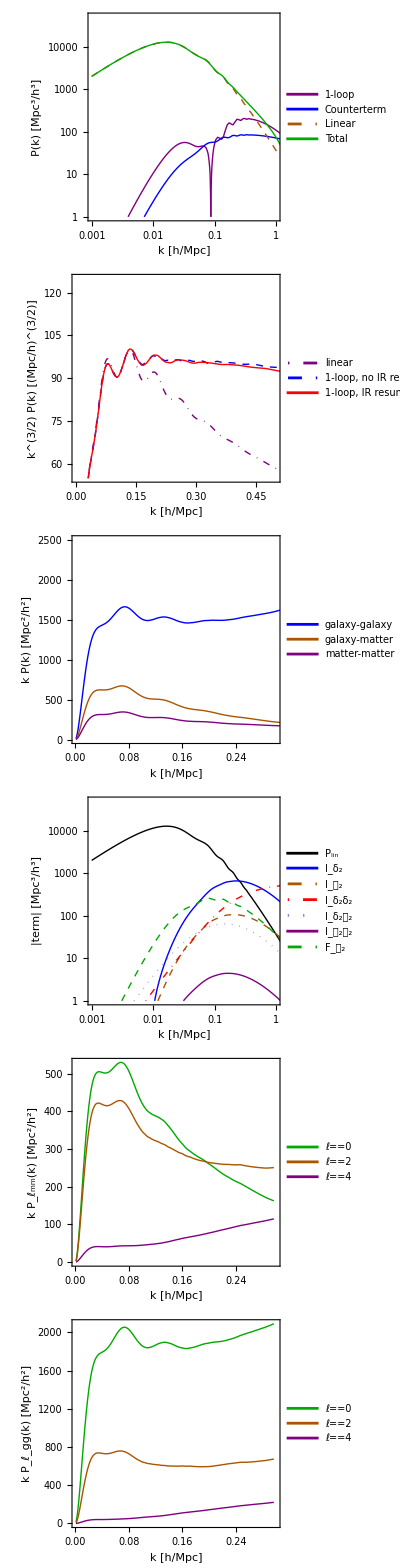

```mathematica
(* Define typesetting helpers, it turns out quite a hassle to set up LaTex-style axis labels and legends in Mathematica *)

logKTicks = {
  {10^-3, TraditionalForm @ Superscript[10, -3]},
  {10^-2, TraditionalForm @ Superscript[10, -2]},
  {10^-1, TraditionalForm @ Superscript[10, -1]},
  {0.3, "0.3"},
  {1, TraditionalForm @ Superscript[10, 0]}
};
kLbl = axisLabel[k, "h"/Mpc];
pLbl = axisLabel[P[k], (Mpc/"h")^3];
kP2Lbl = axisLabel[k P[k], (Mpc/"h")^2];
k32PLbl = axisLabel[
  Row[{Superscript[k, 3/2], " ", P[k]}],
  Superscript[Mpc/"h", 3/2]
];
absTermLbl = axisLabel[TraditionalForm @ Row[{"|term|"}], (Mpc/"h")^3];

pLinLbl = TraditionalForm @ Subscript["P", "lin"];

iD2Lbl   = TraditionalForm @ Subscript[Style["I", Italic], Subscript[δ, 2]];
iG2Lbl   = TraditionalForm @ Subscript[Style["I", Italic], Subscript[𝒢, 2]];
iD2D2Lbl = TraditionalForm @ Subscript[Style["I", Italic], Row[{Subscript[δ, 2], Subscript[δ, 2]}]];
iD2G2Lbl = TraditionalForm @ Subscript[Style["I", Italic], Row[{Subscript[δ, 2], Subscript[𝒢, 2]}]];
iG2G2Lbl = TraditionalForm @ Subscript[Style["I", Italic], Row[{Subscript[𝒢, 2], Subscript[𝒢, 2]}]];
fG2Lbl   = TraditionalForm @ Subscript[Style["F", Italic], Subscript[𝒢, 2]];

pLmmLbl = axisLabel[TraditionalForm @ Row[{k, " ", Subscript[Subscript["P", ℓ], "mm"][k]}], (Mpc/"h")^2];
pLggLbl = axisLabel[TraditionalForm @ Row[{k, " ", Subscript[Subscript["P", ℓ], "gg"][k]}], (Mpc/"h")^2];

(*  Define plots *)

plotMatterBreakdown = ListLogLogPlot[
  {
    Transpose[{kPlot, Abs[pkLoopPlot]}],
    Transpose[{kPlot, Abs[pkCtrPlot]}],
    Transpose[{kPlot, pkTreePlot}],
    Transpose[{kPlot, pkFullPlot}]
  },
  Joined -> True,
  PlotStyle -> {
    Directive[Purple, Thick],
    Directive[Blue, Thick],
    Directive[Darker[Orange], Dashed, Thick],
    Directive[Darker[Green], Thick]
  },
  PlotLegends -> Placed[
    makeLegend[{"1-loop", "Counterterm", "Linear", "Total"}],
    {0.2, 0.8}
  ],
  PlotRange -> {{10^-3, 1}, {1, 5*10^4}},
  Frame -> True,
  FrameTicks -> {{Automatic, None}, {logKTicks, None}},
  FrameLabel -> {kLbl, pLbl},
  ImageSize -> Large
];

plotMatterIR = ListLinePlot[
  {
    Transpose[{kPlot, pkTreePlot kPlot^(3/2)}],
    Transpose[{kPlot, pkFullPlot kPlot^(3/2)}],
    Transpose[{kPlot, pkFullIRPlot kPlot^(3/2)}]
  },
  Joined -> True,
  PlotStyle -> {
    Directive[Purple, DotDashed, Thick],
    Directive[Blue, Dashed, Thick],
    Directive[Red, Thick]
  },
  PlotLegends -> Placed[
    makeLegend[{"linear", "1-loop, no IR resummation", "1-loop, IR resummation"}],
    {0.72, 0.8}
  ],
  PlotRange -> {{10^-3, 0.5}, {55, 125}},
  Frame -> True,
  FrameLabel -> {kLbl, k32PLbl},
  ImageSize -> Large
];

plotRealGGGM = ListLinePlot[
  {
    Transpose[{kPlot, pkGGPlot kPlot}],
    Transpose[{kPlot, pkGMPlot kPlot}],
    Transpose[{kPlot, pkFullIRPlot kPlot}]
  },
  Joined -> True,
  PlotStyle -> {
    Directive[Blue, Thick],
    Directive[Darker[Orange], Thick],
    Directive[Purple, Thick]
  },
  PlotLegends -> Placed[
    makeLegend[{"galaxy-galaxy", "galaxy-matter", "matter-matter"}],
    {0.72, 0.8}
  ],
  PlotRange -> {{10^-3, 0.3}, {1, 2500}},
  Frame -> True,
  FrameLabel -> {kLbl, kP2Lbl},
  ImageSize -> Large
];

plotBasisBreakdown = ListLogLogPlot[
  {
    Transpose[{kPlot, Abs[basisRealFull["P_lin"]]}],
    Transpose[{kPlot, Abs[biasGalaxy["b1"] biasGalaxy["b2"] basisRealFull["I_d2"]]}],
    Transpose[{kPlot, Abs[2 biasGalaxy["b1"] biasGalaxy["bG2"] basisRealFull["I_G2"]]}],
    Transpose[{kPlot, Abs[(biasGalaxy["b2"]^2/4) basisRealFull["I_d2_d2"]]}],
    Transpose[{kPlot, Abs[biasGalaxy["b2"] biasGalaxy["bG2"] basisRealFull["I_d2_G2"]]}],
    Transpose[{kPlot, Abs[biasGalaxy["bG2"]^2 basisRealFull["I_G2_G2"]]}],
    Transpose[{kPlot, Abs[(2 biasGalaxy["b1"] biasGalaxy["bG2"] + (4/5) biasGalaxy["b1"] biasGalaxy["bGamma3"]) basisRealFull["F_G2"]]}]
  },
  Joined -> True,
  PlotStyle -> {
    Directive[Black, Thick],
    Directive[Blue, Thick],
    Directive[Darker[Orange], Dashed, Thick],
    Directive[Red, DotDashed, Thick],
    Directive[Teal, Dotted, Thick],
    Directive[Purple, Thick],
    Directive[Darker[Green], Dashed, Thick]
  },
  PlotLegends -> Placed[
    makeLegend[{pLinLbl, iD2Lbl, iG2Lbl, iD2D2Lbl, iD2G2Lbl, iG2G2Lbl, fG2Lbl}],
    {0.2, 0.78}
  ],
  PlotRange -> {{10^-3, 1}, {1, 5*10^4}},
  Frame -> True,
  FrameTicks -> {{Automatic, None}, {logKTicks, None}},
  FrameLabel -> {kLbl, absTermLbl},
  ImageSize -> Large
];

plotMatterMultipoles = ListLinePlot[
  {
    Transpose[{kPlotRSD, kPlotRSD multipolesMatter["P0"]}],
    Transpose[{kPlotRSD, kPlotRSD multipolesMatter["P2"]}],
    Transpose[{kPlotRSD, kPlotRSD multipolesMatter["P4"]}]
  },
  Joined -> True,
  PlotStyle -> {
    Directive[Darker[Green], Thick],
    Directive[Darker[Orange], Thick],
    Directive[Purple, Thick]
  },
  PlotLegends -> Placed[
    makeLegend[{
      TraditionalForm[ℓ == 0],
      TraditionalForm[ℓ == 2],
      TraditionalForm[ℓ == 4]
    }],
    {0.72, 0.8}
  ],
  PlotRange -> {{10^-3, 0.3}, All},
  Frame -> True,
  FrameLabel -> {kLbl, pLmmLbl},
  ImageSize -> Large
];

plotGalaxyMultipoles = ListLinePlot[
  {
    Transpose[{kPlotRSD, kPlotRSD multipolesGalaxy["P0"]}],
    Transpose[{kPlotRSD, kPlotRSD multipolesGalaxy["P2"]}],
    Transpose[{kPlotRSD, kPlotRSD multipolesGalaxy["P4"]}]
  },
  Joined -> True,
  PlotStyle -> {
    Directive[Darker[Green], Thick],
    Directive[Darker[Orange], Thick],
    Directive[Purple, Thick]
  },
  PlotLegends -> Placed[
    makeLegend[{
      TraditionalForm[ℓ == 0],
      TraditionalForm[ℓ == 2],
      TraditionalForm[ℓ == 4]
    }],
    {0.72, 0.8}
  ],
  PlotRange -> {{10^-3, 0.3}, All},
  Frame -> True,
  FrameLabel -> {kLbl, pLggLbl},
  ImageSize -> Large
];

(* Display plots *)

Column[
  {
    plotMatterBreakdown,
    plotMatterIR,
    plotRealGGGM,
    plotBasisBreakdown,
    plotMatterMultipoles,
    plotGalaxyMultipoles
  },
  Spacings -> 2
]
```